```mathematica
QBO=Import["/users/pp/Desktop/qbo.txt", "table"];  (* qbo20 *)
QBO20=Import["/users/pp/Desktop/qbo20.txt", "table"];
QBO70=Import["/users/pp/Desktop/qbo.txt", "table"];
```

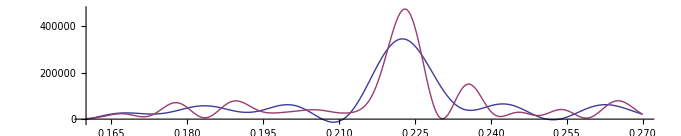

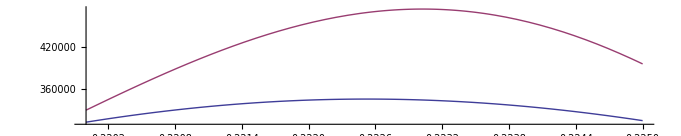

2.34798

2.22335

2.77036

2.94157

1.97584

```mathematica
Q = MeanFilter[QBO[[All,2]],0] - 1*MeanFilter[QBO[[All,2]],320];  (* QBO data 20 hPa *)
QBOT = Table[{QBO[[i,1]], Q[[i]]},{i,1,736,1}];   
QB=ContinuousWaveletTransform[QBOT[[All,2]]];  
Plot[Evaluate@Table[PowerSpectralDensity[Q,ω,i],{i,360,720,360}],{ω,0.16,0.27},PlotRange->All,AspectRatio->0.2]  
Plot[Evaluate@Table[PowerSpectralDensity[Q,ω,i],{i,360,720,360}],{ω,0.22,0.225},PlotRange->All,AspectRatio->0.2]  
2*Pi/0.223/12
2*Pi/0.2355/12
2*Pi/0.189/12
2*Pi/0.178/12
2*Pi/0.265/12
(*
WaveletScalogram[QB, Frame->True, AspectRatio->0.2] 
QBW = 2.3331;
qbombase[x_] := 100*Sin[2*Pi/QBW*x+3.5  ] ;
qbomcomb[x_] := qbombase[x] + 0.3*qbombase[2*x-0.38];
qbom[x_] := qbomcomb[x- 0.24*Sin[2*Pi/18.6*x-4.1] + 0.1*Sin[2*Pi*x-0.8]];
QBOM = Table[{1953.0+x, qbom[73.0+x+0.32]-10},{x,1/12,61.25+1/12, 1/12}]; 
(* QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      *)
OldCC = NewCC; NewCC = 100*Correlation[QBOT,QBOM][[2,2]]; Print[NewCC, "   ", NewCC-OldCC];
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70hPa", "Model"}]
QBM=ContinuousWaveletTransform[QBOM[[All,2]]];  
WaveletScalogram[QBM, Frame->True, AspectRatio->0.2] 

700.0/25.0/12.0
100.0/7.0/12.0
```

{char t,6.19101,-0.0462039, Years from,1881.,to,1982.5,CC,85.3721,85.3743,0.0021383}

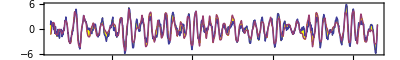

```mathematica
dilate[x_] := Sin[2*Pi*x+1.0];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1230; ENDY=1880+LNGTH/12;  (* 1230 *)
QBW=2.333;     TR = 99.0;  CF = 1.03;  OSC := 18.62;  CW =0.97; 
diu[x_] := 0.2*Cos[2*Pi/(OSC/2)*x+5.3]+0.11*Cos[2*Pi/OSC*x+0.5] -0*0.12*Sin[2*Pi/4.426*x-1.1];
qbase[x_]:=0.19*Cos[2*Pi/QBW*x+2.9-0.24*Sin[2*Pi/OSC*x-0.4] + 0.1*Sin[2*Pi*x-0.3]+ 0.02*Sin[4*Pi*x-1.3]];
SMALL=1;
qbw[x_] := qbase[x]*(1-0.26*Sin[2*Pi/10.58*x-1.43]) +  
(* qbw[x_] := qbom[x+0.35]*(1-0.26*Sin[2*Pi/10.58*x-1.43])*0.0014 +  *)
           0.1*Sin[2*Pi/2.246*x+0.02-0.1*Sin[2*Pi/OSC*x-0.4]] -
           SMALL*0.032*Cos[2*Pi/2.11*x-1.4] - 
           SMALL*0.05*Cos[2*Pi/3.575*x-1.77+0.5*Sin[2*Pi/OSC*x+1.3]]-  
           SMALL*0.04*Cos[2*Pi/1.94*x-2.0] + SMALL*0.01*Cos[2*Pi/7*x-3] -
           SMALL*0.06*Cos[2*Pi/4.04*x-1.89+0.52*Sin[2*Pi/OSC*x+2.3]] -
           SMALL*0.06*Cos[2*Pi/2.78*x-2.2+0.57*Sin[2*Pi/OSC*x+0.67]] -
           0.152*Cos[2*Pi/2.9*x-0.8+0.57*Sin[2*Pi/OSC*x+0.67] - 0.18*Sin[2*Pi/4.422*x+0.1]]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := 0.27*cw[x+1.6]+0*.13*cw[x/2+1.5] + 0*.03*Cos[2*Pi/5.8*x+4.0] ;  
RHS[x_] := (8.3*qbw[x*1.001-0.15]*(1-0.19*Sin[2*Pi/OSC*x+1.2]) +0.31*cwb[x+1.0]-1.3*diu[x-0.7] ) + 0.11*Cos[2*Pi/52*x-1.9] - 0.2*Cos[2*Pi/7.33*x-0.7];  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},    {x,STRT/12,LNGTH/12, 1/12}]; 
LOW = 100.2; HI = 116.3;    
rhs=Table[{1880.0+x, If[x>LOW&&x<HI,-0.7,0]-If[x>LOW&&x<HI,-1,1]*1.17*RHS[x-0.1*dilate[x]+0.83]},   {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.15]
```